```mathematica
Integrate[E^(-Abs[x+y]/u),{x,-w,w},Assumptions->Element[w,Reals]&&Element[y,Reals]&&w>0]
```

Piecewise[{{ⅇ^(-w/u-y/u) (-1+ⅇ^((2 w)/u)) u, w-y<0&&w>0&&w+y>0}, {-ⅇ^(-w/u-y/u) (1+ⅇ^((2 y)/u)-2 ⅇ^(w/u+y/u)) u, w-y>0&&w>0&&w+y>0}, {ⅇ^(-w/u-y/u) (-1+ⅇ^(w/u+y/u)) u, w-y==0&&w>0&&w+y>0}, {2 ⅇ^(y/u) u Sinh[w/u], True}}]

```mathematica
Clear[f]
```

```mathematica
f[y_,u_,w_]:=Piecewise[{{ⅇ^(-w/u-y/u) (-1+ⅇ^((2 w)/u)) u, w-y<0&&w>0&&w+y>0}, {-ⅇ^(-w/u-y/u) (1+ⅇ^((2 y)/u)-2 ⅇ^(w/u+y/u)) u, w-y>0&&w>0&&w+y>0}, {ⅇ^(-w/u-y/u) (-1+ⅇ^(w/u+y/u)) u, w-y==0&&w>0&&w+y>0}, {2 ⅇ^(y/u) u Sinh[w/u], True}}]
```

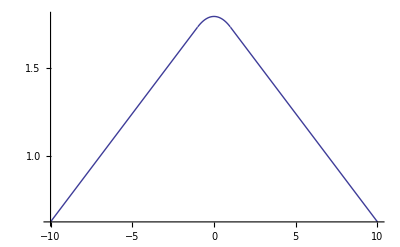

```mathematica
LogPlot[f[x,10.,1.],{x,-10,10}]
```